# Clasificador logístico

### Carlos Manuel Rodríguez Martínez 3/07/2020

Cargar base de datos Iris

Carga toda la base de datos Iris

```mathematica
{attributes,rawDatabase} = TakeDrop[Import[FileNameJoin[{NotebookDirectory[],"iris.csv"}]],1];
```

```mathematica
attributes
```

{{sepal-length,sepal-width,petal-length,petal-width,species}}

Selecciona las clases setosa y virginica, y toma solo el atributo sepal-length

```mathematica
processedDatabase = Cases[rawDatabase,{_,_,_,_,"setosa"}|{_,_,_,_,"virginica"}][[All,{1,-1}]]
```

{{5.1,setosa},{4.9,setosa},{4.7,setosa},{4.6,setosa},{5.,setosa},{5.4,setosa},{4.6,setosa},{5.,setosa},{4.4,setosa},{4.9,setosa},{5.4,setosa},{4.8,setosa},{4.8,setosa},{4.3,setosa},{5.8,setosa},{5.7,setosa},{5.4,setosa},{5.1,setosa},{5.7,setosa},{5.1,setosa},{5.4,setosa},{5.1,setosa},{4.6,setosa},{5.1,setosa},{4.8,setosa},{5.,setosa},{5.,setosa},{5.2,setosa},{5.2,setosa},{4.7,setosa},{4.8,setosa},{5.4,setosa},{5.2,setosa},{5.5,setosa},{4.9,setosa},{5.,setosa},{5.5,setosa},{4.9,setosa},{4.4,setosa},{5.1,setosa},{5.,setosa},{4.5,setosa},{4.4,setosa},{5.,setosa},{5.1,setosa},{4.8,setosa},{5.1,setosa},{4.6,setosa},{5.3,setosa},{5.,setosa},{6.3,virginica},{5.8,virginica},{7.1,virginica},{6.3,virginica},{6.5,virginica},{7.6,virginica},{4.9,virginica},{7.3,virginica},{6.7,virginica},{7.2,virginica},{6.5,virginica},{6.4,virginica},{6.8,virginica},{5.7,virginica},{5.8,virginica},{6.4,virginica},{6.5,virginica},{7.7,virginica},{7.7,virginica},{6.,virginica},{6.9,virginica},{5.6,virginica},{7.7,virginica},{6.3,virginica},{6.7,virginica},{7.2,virginica},{6.2,virginica},{6.1,virginica},{6.4,virginica},{7.2,virginica},{7.4,virginica},{7.9,virginica},{6.4,virginica},{6.3,virginica},{6.1,virginica},{7.7,virginica},{6.3,virginica},{6.4,virginica},{6.,virginica},{6.9,virginica},{6.7,virginica},{6.9,virginica},{5.8,virginica},{6.8,virginica},{6.7,virginica},{6.7,virginica},{6.3,virginica},{6.5,virginica},{6.2,virginica},{5.9,virginica}}

Se termina el preprocesamiento cambiando las etiquetas setosa a 1, y virginica a 0.

```mathematica
processedDatabase = ReplaceAll[processedDatabase,{"setosa"->1,"virginica"->0}]
```

{{5.1,1},{4.9,1},{4.7,1},{4.6,1},{5.,1},{5.4,1},{4.6,1},{5.,1},{4.4,1},{4.9,1},{5.4,1},{4.8,1},{4.8,1},{4.3,1},{5.8,1},{5.7,1},{5.4,1},{5.1,1},{5.7,1},{5.1,1},{5.4,1},{5.1,1},{4.6,1},{5.1,1},{4.8,1},{5.,1},{5.,1},{5.2,1},{5.2,1},{4.7,1},{4.8,1},{5.4,1},{5.2,1},{5.5,1},{4.9,1},{5.,1},{5.5,1},{4.9,1},{4.4,1},{5.1,1},{5.,1},{4.5,1},{4.4,1},{5.,1},{5.1,1},{4.8,1},{5.1,1},{4.6,1},{5.3,1},{5.,1},{6.3,0},{5.8,0},{7.1,0},{6.3,0},{6.5,0},{7.6,0},{4.9,0},{7.3,0},{6.7,0},{7.2,0},{6.5,0},{6.4,0},{6.8,0},{5.7,0},{5.8,0},{6.4,0},{6.5,0},{7.7,0},{7.7,0},{6.,0},{6.9,0},{5.6,0},{7.7,0},{6.3,0},{6.7,0},{7.2,0},{6.2,0},{6.1,0},{6.4,0},{7.2,0},{7.4,0},{7.9,0},{6.4,0},{6.3,0},{6.1,0},{7.7,0},{6.3,0},{6.4,0},{6.,0},{6.9,0},{6.7,0},{6.9,0},{5.8,0},{6.8,0},{6.7,0},{6.7,0},{6.3,0},{6.5,0},{6.2,0},{5.9,0}}

Propiedades de los datos

Histograma de la longitud del sépalo para las especies setosa y virginica.

```mathematica
onlySetosa = Cases[rawDatabase,{_,_,_,_,"setosa"}][[All,{1,-1}]]/.{"setosa"->1,"virginica"->0};
onlyVirginica = Cases[rawDatabase,{_,_,_,_,"virginica"}][[All,{1,-1}]]/.{"setosa"->1,"virginica"->0};
```

```mathematica
sepalLengthSetosa = onlySetosa[[All,1]];
sepalLengthVirginica = onlyVirginica[[All,1]];
```

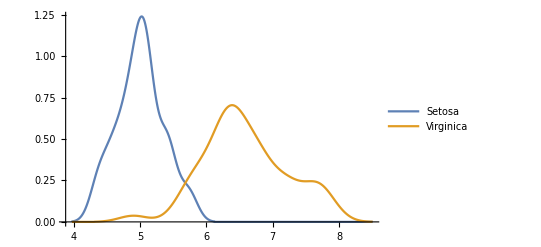

```mathematica
SmoothHistogram[{sepalLengthSetosa,sepalLengthVirginica},PlotLegends->{"Setosa","Virginica"}]
```

Regresión logística

Se utilizó el algoritmo iterativo que se describe en la ecuación
-Graphics-
del libro de Bishop.

```mathematica
PhiDesignMatrix[data_]:=Map[{1,#}&,data];
ClassificationProbability[x_,w_]:=LogisticSigmoid[w.{1,x}];

NewW[x_,t_,wOld_]:=Block[{y,RMatrix,zVector},
y = Map[ClassificationProbability[#,wOld]&,x];
RMatrix=DiagonalMatrix[y(1-y)];
zVector = PhiDesignMatrix[x].wOld-Inverse[RMatrix].(y-t);

Inverse[Transpose[PhiDesignMatrix[x]].RMatrix.PhiDesignMatrix[x]].Transpose[PhiDesignMatrix[x]].RMatrix.zVector
];
```

Se comienza con un peso inicial w0 = {0,0}.

```mathematica
x = processedDatabase[[All,1]];
t = processedDatabase[[All,2]];
w0 = {0,0};
```

La función NewW devuelve el nuevo valor de w.

```mathematica
NewW[x,t,w0]
```

{10.3662,-1.78819}

Se itera 10 veces

```mathematica
ws = Drop[NestList[NewW[x,t,#]&,w0,10],1]
```

{{10.3662,-1.78819},{17.996,-3.13951},{25.8628,-4.54225},{32.9298,-5.80414},{37.2984,-6.5829},{38.4807,-6.79309},{38.5467,-6.80479},{38.5469,-6.80482},{38.5469,-6.80482},{38.5469,-6.80482}}

A continuación se muestran las fronteras óptimas y las gráficas para las 10 iteraciones.

```mathematica
CalculateFrontier[w_]:=First[xt /. Quiet @Solve[ClassificationProbability[xt,w]==0.5,xt]];
PlotLogisticClassifier[w_]:=Show[
ListPlot[
{onlySetosa,onlyVirginica},
PlotRange->{{0,10},{-0.1,1.1}},PlotLegends->{"Setosa","Virginica"},
ImageSize->400,
PlotTheme->"Monochrome",
FrameLabel->{"Sepal length","P(Setosa | Sepal length)"},
Frame->True,
PlotMarkers->None, 
PlotStyle->{RGBColor[0., 0.76, 0.33],RGBColor[0.9, 0.05, 0.]},
GridLines->{{CalculateFrontier[w]},{0.5}},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLabel->w
],
Plot[
{ClassificationProbability[xt,w],1-ClassificationProbability[xt,w]},{xt,0,10},
PlotStyle->{RGBColor[0., 0.76, 0.33],RGBColor[0.9, 0.05, 0.]},
PlotLegends->{"P(Setosa|Sepal length)","P(Virginica|Sepal length)"}
]
];
```

Para calcular la frontera óptima se busca el valor de la longitud de sépalo que da una probabilidad igual a 0.5. Se muestran las fronteras óptimas por iteración.

```mathematica
frontiers = Map[CalculateFrontier,ws]
```

{5.797,5.73209,5.69382,5.67351,5.66595,5.66469,5.66465,5.66465,5.66465,5.66465}

```mathematica
bestFrontier = Last[frontiers]
```

5.66465

Posición de la frontera óptima en el histograma de los datos por cada iteración. En la etiqueta se muestra el valor de w.

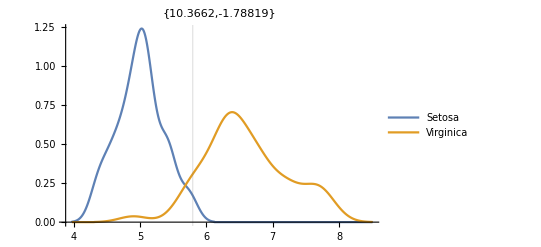
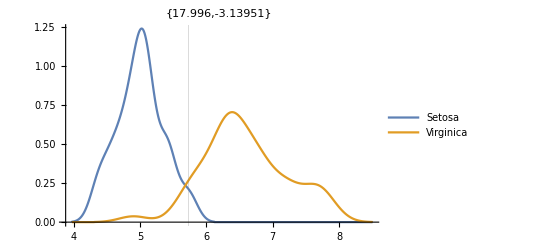
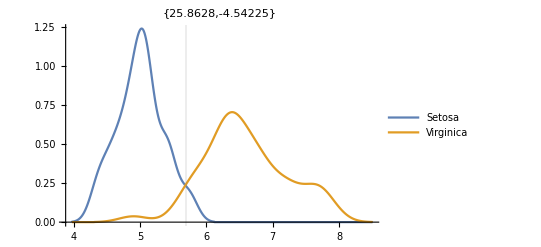
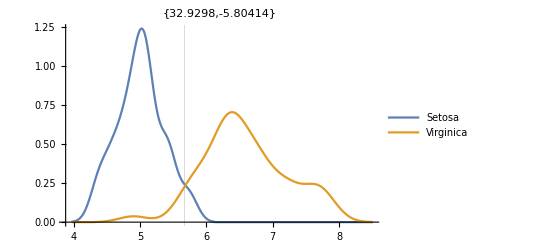
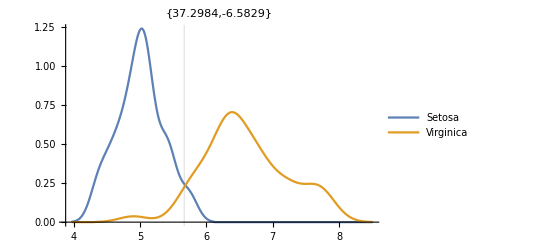
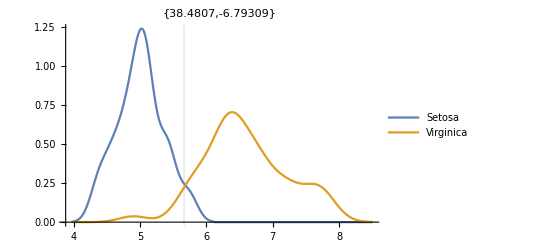
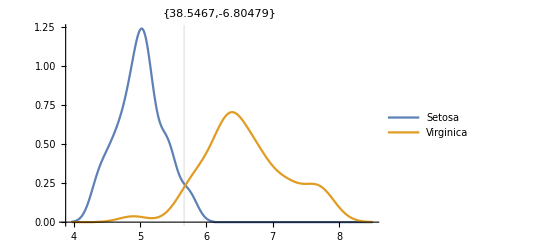
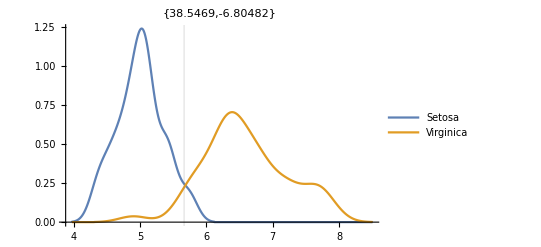
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MapThread[
SmoothHistogram[{sepalLengthSetosa,sepalLengthVirginica},PlotLegends->{"Setosa","Virginica"},GridLines->{{#1}},PlotLabel->#2]&,
{frontiers,ws}
]
```

Gráficas de los modelos logísticos en cada iteración. En la etiqueta se muestra el valor de w. La línea vertical representa la posición de la frontera óptima, mientras que la línea horizontal representa el valor de probabilidad 0.5 a partir del cual se calculó la frontera óptima.

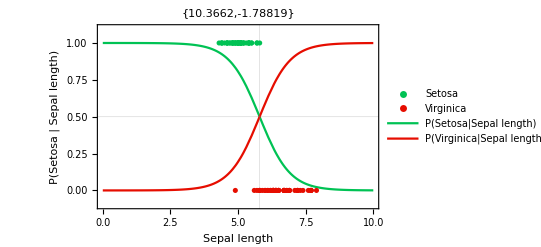
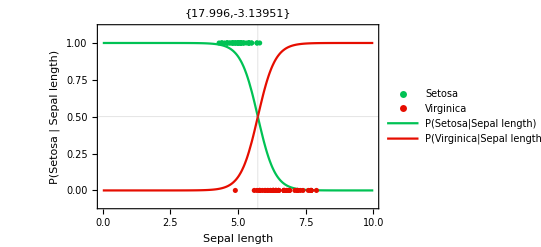
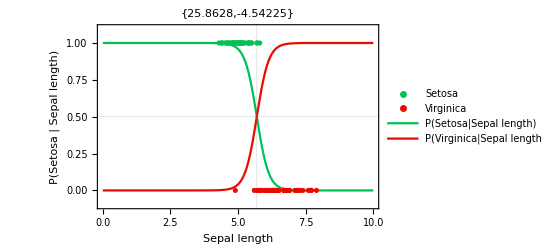
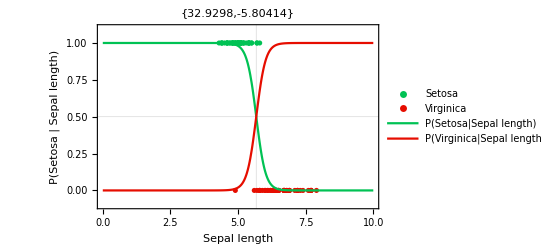
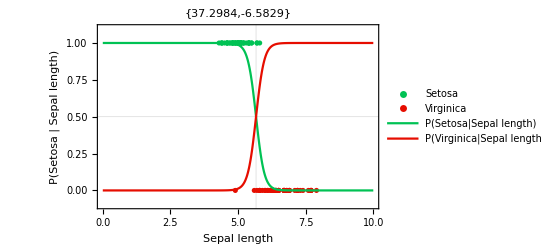
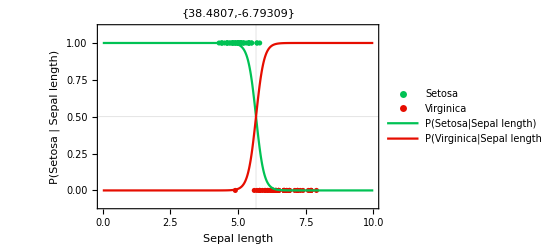
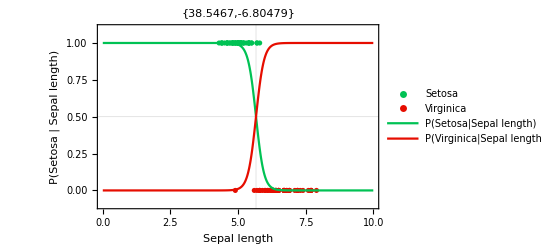
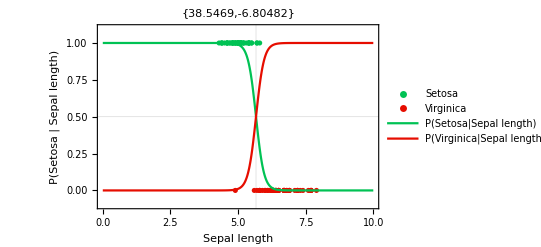
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[PlotLogisticClassifier,ws]
```

Tasa de clasificación

El clasificador clasifica correctamente el 94% de las especies setosa

```mathematica
truePositives = N@(Count[onlySetosa[[All,1]],x_/;x<bestFrontier]/Length[onlySetosa[[All,1]]])
```

0.94

sin embargo clasifica incorrectamente como setosa el 4% de las especies virginica

```mathematica
falsePositives = N@ (Count[onlyVirginica[[All,1]],x_/;x<bestFrontier]/Length[onlySetosa[[All,1]]])
```

0.04

De la especie virgínica, clasifica incorretamente el 6% como setosa

```mathematica
falseNegatives = N@ (Count[onlySetosa[[All,1]],x_/;x>bestFrontier]/Length[onlyVirginica[[All,1]]])
```

0.06

Y clasifica correctamente el 96% de las especies virgínica.

```mathematica
trueNegatives = N@ (Count[onlyVirginica[[All,1]],x_/;x>bestFrontier]/Length[onlyVirginica[[All,1]]])
```

0.96